H={0.577552, 3.21443, 11.4517, -0.448729, 0.233417, 8.69148, 12.5331, 13.0909, 10.8223, 10.5191}

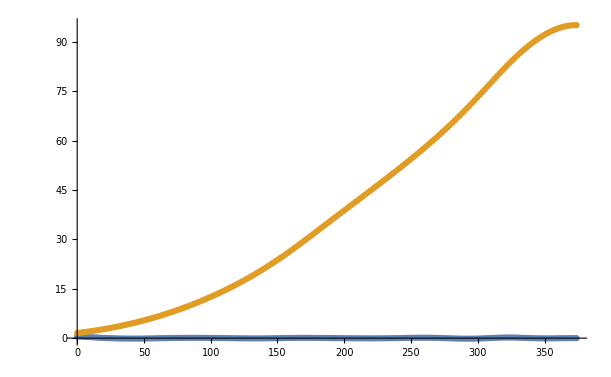

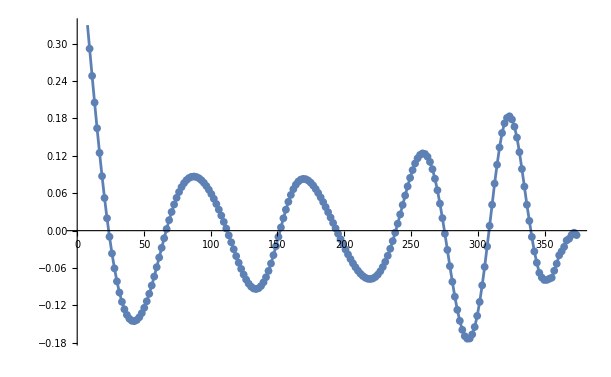

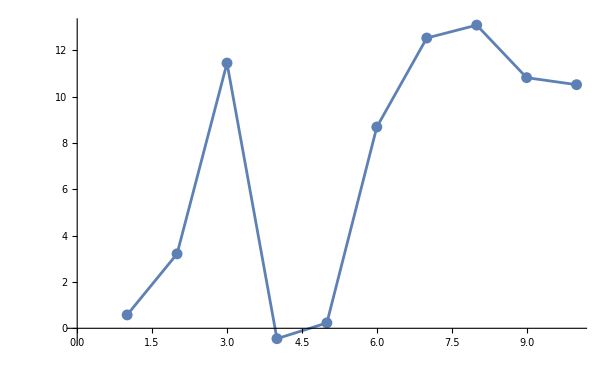

```mathematica
(*获取当前 Notebook 的目录*)
currentDirectory=NotebookDirectory[];
(*设置当前工作目录为 Notebook 目录*)
SetDirectory[currentDirectory];

Inputdata =Table[ToExpression[ Partition[StringReplace[StringSplit[Import["data\\" <> ToString[i] <>".txt"]],"e"->"*10^"],2]],{i,1,10,1}];
HeatNum = 10;
DataxNum = Length[Inputdata[[1]]];
M=Table[Inputdata[[i]][[j]][[2]],{i,1,10,1},{j,1,DataxNum,1}]*10^9//Transpose;
Inputdata =ToExpression[ Partition[StringReplace[StringSplit[Import["data\\heat source.txt"]],"e"->"*10^"],2]];
datax = Map[First,Inputdata]*10^3;
K= -Map[Last,Inputdata]*10^9;
H=LeastSquares[M,K];
Print["H="<>ToString[H]]

ListPlot[{Partition[Riffle[datax,M.H-K],2],Partition[Riffle[datax,-K],2]},Mesh->All,Joined->True]
ListPlot[Partition[Riffle[datax,M.H-K],2],Mesh->All,Joined->True]
ListPlot[{H},Mesh->All,Joined->True]
```

```mathematica
x=Table[0,{i,1,10}]
```

{0,0,0,0,0,0,0,0,0,0}

```mathematica
Transpose[M].(K-M.x)
```

{-31707.5,-29033.2,-27497.4,-26609.7,-22310.9,-2412.89,5180.34,15241.3,26678.2,37978.5}

```mathematica
Length[%19]
```

202

```mathematica
{1,2,3}.{1,2,3}
```

14

```mathematica
Dot[{1,2,3},{1,2,3}]
```

14

```mathematica
AbsoluteTiming[H=LeastSquares[M,K];][[1]]
```

0.0005888

```mathematica
t=0
Table[t+=AbsoluteTiming[H=LeastSquares[M,K];][[1]],{i,1,1000}];
t/1000
```

0

0.000139774

```mathematica
useTime={1.871,1.319,4.176,0.5371,0.4178,0.4746,1.019}
```

{1.871,1.319,4.176,0.5371,0.4178,0.4746,1.019}

```mathematica
useTimeBar=BarChart[<|"Python"->useTime[[3]], "MATLAB"->useTime[[1]], "C++: Eigen"->useTime[[2]], "C++: NNLS"->useTime[[7]], "Mathematica:\nQR_MGS"->useTime[[4]], "C++: QR_MGS"->useTime[[6]], "C++:\nnormal_equation"->useTime[[5]]|>,GridLines->{None,Range[0,4],None},GridLinesStyle->Directive[Thickness[0.0015],Black,Dotted],AxesLabel->{Style["",Bold,Black,FontSize->15],Style[HoldForm["Using time [ms]"],Bold,Black,FontSize->20]},AxesStyle->Directive[Thickness[0.0015],Black,12],ChartLabels->Callout[Automatic,Above],ChartStyle->"GrayYellowTones",LabelStyle->Directive[Medium,Black,Bold],ImageSize->UpTo[1000]]
```

-Graphics-

```mathematica
Export["C:\\Users\\Lenovo\\Desktop\\XFEL\\deflecting\\MHCKF\\data\\using time.png",useTimeBar,"PNG",ImageResolution->1000]
```

C:\Users\Lenovo\Desktop\XFEL\deflecting\MHCKF\data\using time.png